```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.01,1,0]],A:=Inverse[β[ω,0.01,1,0]],B:=Inverse[β[ω,0.01,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T1.Inverse[IdentityMatrix[1]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
LEFT1[ω_,δ_,t_,ϵ_,N_]:=Module[{J=Inverse[β[ω,0.01,1,0]],A:=Inverse[β[ω,0.01,1,0]],B:=Inverse[β[ω,0.01,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T1.Inverse[IdentityMatrix[1]-B.T2.J.T2].B.T1].A,N];J=J]
```

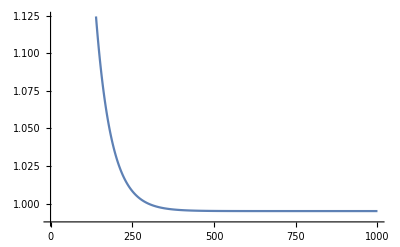

```mathematica
ListLinePlot[Table[{N,-Im[LEFT1[0,0.001,1,0,N][[1,1]]]},{N,10,1000}]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0,0.001,1,0]
```

0.999984

```mathematica
g[0,0.001,1,0]
```

{{0.-1000. ⅈ}}

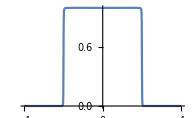

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.001,1,0]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
device1[ω_,δ_,t_,ϵ_]:= Module[{j=LEFT[ω,δ,t,ϵ],g=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1]},Do[j=Inverse[IdentityMatrix[1]-g.T.j.T].g,9];j=j]
```

```mathematica
device2[ω_,δ_,t_,ϵ_,ϵ1_]:=
```

```mathematica
device1[0,0.01,1,0+0.02]
```

{{-0.0115116-0.99828 ⅈ}}

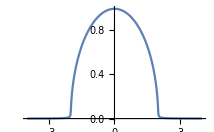

```mathematica
ListLinePlot[Table[{ω,-Im[device1[ω,0.01,1,0][[1,1]]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
ϕ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=device1[ω,δ,t,ϵ]},
Il1:=Inverse[IdentityMatrix[1]-g.T1[t].SR[ω,δ,t,0].T1[t]].g;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,0].T1[t].g.T1[t]].SR[ω,δ,t,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,0].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

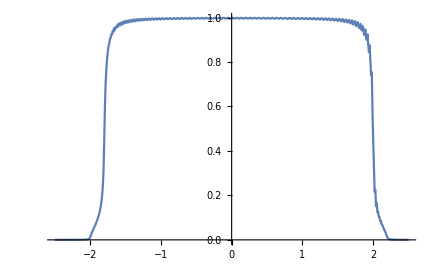

```mathematica
ListLinePlot[Table[{ω,ϕ[ω,0.01,1,0.2,0]},{ω,Range[-2.5,2.5,0.01]}]]
```